```mathematica
ConCases = Import["https://raw.githubusercontent.com/CSSEGISandData/COVID-19/master/csse_covid_19_data/csse_covid_19_time_series/time_series_19-covid-Confirmed.csv","CSV"];
ConDeaths = Import["https://raw.githubusercontent.com/CSSEGISandData/COVID-19/master/csse_covid_19_data/csse_covid_19_time_series/time_series_19-covid-Deaths.csv","CSV"];
States = Table[ConCases[[i,1]],{i,2,Length[ConCases]}];
```

```mathematica
DatesTab = Table[ConCases[[1,i]],{i,5,Length[ConCases[[1]]]}];
Dates = Table[DateList[{DatesTab[[i]],{"Month","/","Day","/","YearShort"}}],{i,1,Length[DatesTab]}];
Countries = Table[ConCases[[i,2]],{i,2,Length[ConCases]}];
```

```mathematica
Countries
```

{Thailand,Japan,Singapore,Nepal,Malaysia,Canada,Australia,Australia,Australia,Cambodia,Sri Lanka,Germany,Finland,United Arab Emirates,Philippines,India,Italy,Sweden,Spain,Australia,Belgium,Egypt,Australia,Lebanon,Iraq,Oman,Afghanistan,Bahrain,Kuwait,Algeria,Croatia,Switzerland,Austria,Israel,Pakistan,Brazil,Georgia,Greece,North Macedonia,Norway,Romania,Estonia,San Marino,Belarus,Iceland,Lithuania,Mexico,New Zealand,Nigeria,Australia,Ireland,Luxembourg,Monaco,Qatar,Ecuador,Azerbaijan,Armenia,Dominican Republic,Indonesia,Portugal,Andorra,Australia,Latvia,Morocco,Saudi Arabia,Senegal,Argentina,Chile,Jordan,Ukraine,Hungary,Australia,Liechtenstein,Poland,Tunisia,Bosnia and Herzegovina,Slovenia,South Africa,Bhutan,Cameroon,Colombia,Costa Rica,Peru,Serbia,Slovakia,Togo,Malta,Martinique,Bulgaria,Maldives,Bangladesh,Paraguay,Canada,Canada,Canada,Albania,Cyprus,Brunei,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,Burkina Faso,Holy See,Mongolia,Panama,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,China,Iran,Korea, South,France,China,China,China,China,China,China,China,Cruise Ship,China,China,China,China,Denmark,China,China,China,China,China,China,China,China,China,China,China,China,China,China,China,Czechia,China,China,China,Taiwan*,Vietnam,Russia,China,China,Moldova,Bolivia,Denmark,France,Honduras,United Kingdom,Canada,China,Congo (Kinshasa),Cote d'Ivoire,France,Jamaica,Turkey,United Kingdom,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,US,Cuba,Guyana,Australia,United Kingdom,Kazakhstan,France,Canada,Canada,Ethiopia,Sudan,Guinea,Canada,Kenya,Antigua and Barbuda,US,Uruguay,Ghana,US,Namibia,Seychelles,Trinidad and Tobago,Venezuela,Eswatini,Gabon,Guatemala,Mauritania,Rwanda,Saint Lucia,Saint Vincent and the Grenadines,Suriname,France,US,Kosovo,Canada,Canada,Central African Republic,Congo (Brazzaville),Equatorial Guinea,France,Uzbekistan,Netherlands,Canada,France,Benin,Greenland,Liberia,Netherlands,Somalia,Tanzania,The Bahamas,US,United Kingdom,France,Barbados,Montenegro,Kyrgyzstan,Mauritius,Netherlands,Zambia,Djibouti,Gambia, The,United Kingdom,Guadeloupe,Reunion,French Guiana,Aruba,Bahamas, The,Mayotte,Denmark,France,US,United Kingdom,Chad,El Salvador,Fiji,Nicaragua,US,Guam,Guernsey,Jersey,Puerto Rico,Republic of the Congo,The Gambia}

## France

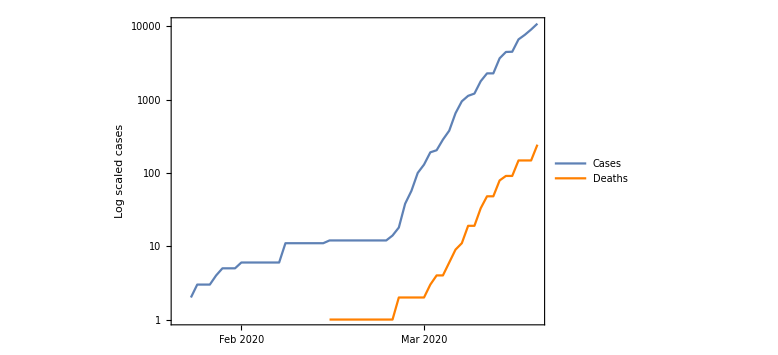

Cases multiplied by 2.7 every 4.28 Days, based on last data from last 15 days

```mathematica
NofDays =15;(* Number of days the fit routine uses to calculate rate*)
Lookfor = "France";
ind = Position[Countries,Lookfor][[1,1]];
ConCasest =Table[ConCases[[ind+1,i]],{i,5,Length[ConCases[[ind+1]]]}];
countrydatacases= Table[{Dates[[i]],ConCasest[[i]]},{i,1,Length[ConCasest]}];
ConDeathst =Table[ConDeaths[[ind+1,i]],{i,5,Length[ConDeaths[[ind+1]]]}];
countrydatadeaths= Table[{Dates[[i]],ConDeathst[[i]]},{i,1,Length[ConDeathst]}];
Show[DateListLogPlot[countrydatacases,PlotLegends->LineLegend[{"Cases"}],DateTicksFormat->{"Day","/","MonthShort"}],DateListLogPlot[countrydatadeaths,PlotStyle->Orange,PlotLegends->LineLegend[{"Deaths"}],PlotRange->All,DateTicksFormat->{"Day","/","MonthShort"}],Frame-> True,FrameLabel->{"","Log scaled cases"},LabelStyle->Directive[16,Black],ImageSize-> Large]
Logcases= Table[{i - (Length[ConCasest]-NofDays),N[Log[ConCasest[[i]]]]},{i,Length[ConCasest]-NofDays,Length[ConCasest]}];
line=Fit[Logcases,{1,x},x];
Print[Style["Cases multiplied by 2.7 every "<> ToString[Round[1/line[[2,1]],0.01]]<>" Days, based on last data from last " <> ToString[NofDays] <>" days ",20,Purple,FontFamily->"Times New Roman"]]
```

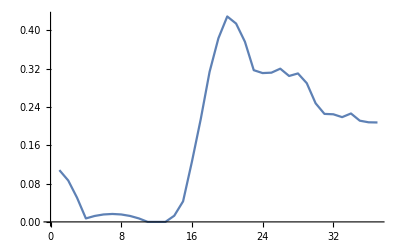

```mathematica
Propagationrate = Table[Logcases= Table[{i,N[Log[ConCasest[[i]]]]},{i,j,j+7}];
line=Fit[Logcases,{1,x},x][[2,1]],{j,15,Length[ConCasest] - 7}];
ListLinePlot[Propagationrate]
```

```mathematica
(* We can calculate roughly based on the slope of the curve how much time of confinement left if the virus keeps spreading like this, x is the number of days of total confinement *)
```

```mathematica
DaysSinceSeriousMeasures =6;
Solve[Fit[Table[Propagationrate[[i]],{i,Length[Propagationrate]-DaysSinceSeriousMeasures,Length[Propagationrate]}],{1,x},x] == 0,x]
```

{{x→68.3239}}

## UK

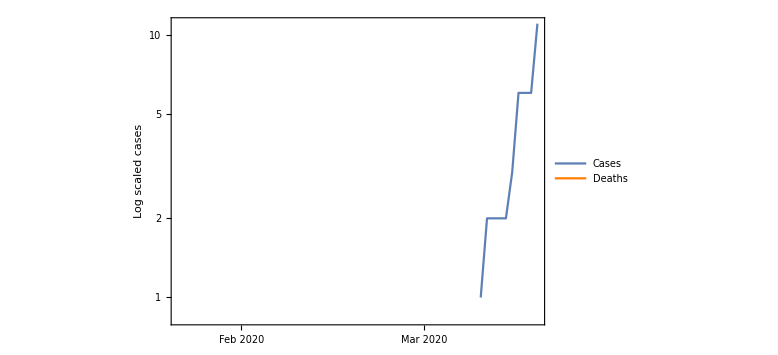

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Cases multiplied by 2.7 every 1. Days, based on last data from last 15 days

```mathematica
NofDays =15;(* Number of days the fit routine uses to calculate rate*)
Lookfor = "United Kingdom";
ind = Position[Countries,Lookfor][[1,1]];
ConCasest =Table[ConCases[[ind+1,i]],{i,5,Length[ConCases[[ind+1]]]}];
countrydatacases= Table[{Dates[[i]],ConCasest[[i]]},{i,1,Length[ConCasest]}];
ConDeathst =Table[ConDeaths[[ind+1,i]],{i,5,Length[ConDeaths[[ind+1]]]}];
countrydatadeaths= Table[{Dates[[i]],ConDeathst[[i]]},{i,1,Length[ConDeathst]}];
Show[DateListLogPlot[countrydatacases,PlotLegends->LineLegend[{"Cases"}],DateTicksFormat->{"Day","/","MonthShort"}],DateListLogPlot[countrydatadeaths,PlotStyle->Orange,PlotLegends->LineLegend[{"Deaths"}],PlotRange->All,DateTicksFormat->{"Day","/","MonthShort"}],Frame-> True,FrameLabel->{"","Log scaled cases"},LabelStyle->Directive[16,Black],ImageSize-> Large]
Logcases= Table[{i - (Length[ConCasest]-NofDays),N[Log[ConCasest[[i]]]]},{i,Length[ConCasest]-NofDays,Length[ConCasest]}];
line=Fit[Logcases,{1,x},x];
Print[Style["Cases multiplied by 2.7 every "<> ToString[Round[1/line[[2,1]],0.01]]<>" Days, based on last data from last " <> ToString[NofDays] <>" days ",20,Purple,FontFamily->"Times New Roman"]]
```

```mathematica
(*Rate of disease propagation over time, (if the propagation is exponential this is tau in Exp[t/tau], or it is the change of slope of the previous curve calculated over a week), in Italy confinement started to work about a week ago but the propagation is not slowing as it should *)
```

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of Fit::fitm will be suppressed during this calculation.

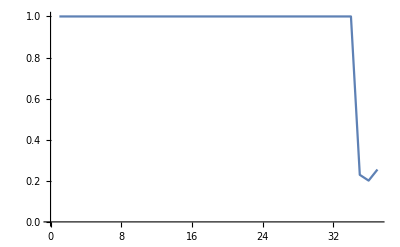

```mathematica
ListLinePlot[Table[Logcases= Table[{i,N[Log[ConCasest[[i]]]]},{i,j,j+7}];
line=Fit[Logcases,{1,x},x][[2,1]],{j,15,Length[ConCasest] -7}]]
```

```mathematica
(* We can calculate roughly based on the slope of the curve how much time of confinement left if the virus keeps spreading like this, x is the number of days of total confinement *)
```

```mathematica
DaysSinceSeriousMeasures = 9;
Solve[Fit[Table[Propagationrate[[i]],{i,Length[Propagationrate]-DaysSinceSeriousMeasures,Length[Propagationrate]}],{1,x},x] == 0,x]
```

{{x→28.7972}}

## Italy

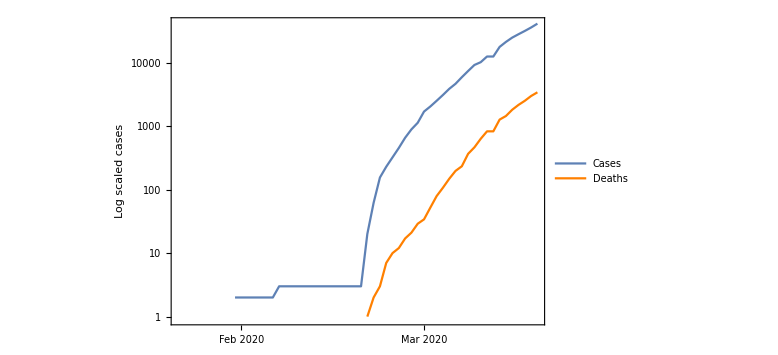

Cases multiplied by 2.7 every 5.8 Days, based on last data from last 15 days

```mathematica
NofDays =15;(* Number of days the fit routine uses to calculate rate*)
Lookfor = "Italy";
ind = Position[Countries,Lookfor][[1,1]];
ConCasest =Table[ConCases[[ind+1,i]],{i,5,Length[ConCases[[ind+1]]]}];
countrydatacases= Table[{Dates[[i]],ConCasest[[i]]},{i,1,Length[ConCasest]}];
ConDeathst =Table[ConDeaths[[ind+1,i]],{i,5,Length[ConDeaths[[ind+1]]]}];
countrydatadeaths= Table[{Dates[[i]],ConDeathst[[i]]},{i,1,Length[ConDeathst]}];
Show[DateListLogPlot[countrydatacases,PlotLegends->LineLegend[{"Cases"}],DateTicksFormat->{"Day","/","MonthShort"}],DateListLogPlot[countrydatadeaths,PlotStyle->Orange,PlotLegends->LineLegend[{"Deaths"}],PlotRange->All,DateTicksFormat->{"Day","/","MonthShort"}],Frame-> True,FrameLabel->{"","Log scaled cases"},LabelStyle->Directive[16,Black],ImageSize-> Large]
Logcases= Table[{i - (Length[ConCasest]-NofDays),N[Log[ConCasest[[i]]]]},{i,Length[ConCasest]-NofDays,Length[ConCasest]}];
line=Fit[Logcases,{1,x},x];
Print[Style["Cases multiplied by 2.7 every "<> ToString[Round[1/line[[2,1]],0.01]]<>" Days, based on last data from last " <> ToString[NofDays] <>" days ",20,Purple,FontFamily->"Times New Roman"]]
```

```mathematica
(*Rate of disease propagation over time, (if the propagation is exponential this is tau in Exp[t/tau], or it is the change of slope of the previous curve calculated over a week), in Italy confinement started to work about a week ago but the propagation is not slowing as it should *)
```

Part::partd: Part specification 1.09861⟦2,1⟧ is longer than depth of object.

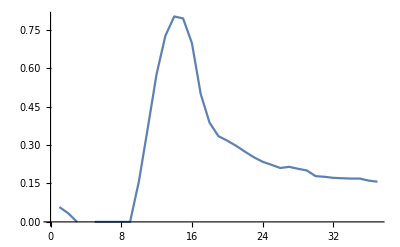

```mathematica
ListLinePlot[Table[Logcases= Table[{i,N[Log[ConCasest[[i]]]]},{i,j,j+7}];
line=Fit[Logcases,{1,x},x][[2,1]],{j,15,Length[ConCasest] -7}]]
```

```mathematica
(* We can calculate roughly based on the slope of the curve how much time of confinement left if the virus keeps spreading like this, x is the number of days of total confinement *)
```

```mathematica
DaysSinceSeriousMeasures = 9;
Solve[Fit[Table[Propagationrate[[i]],{i,Length[Propagationrate]-DaysSinceSeriousMeasures,Length[Propagationrate]}],{1,x},x] == 0,x]
```

{{x→28.7972}}

## China

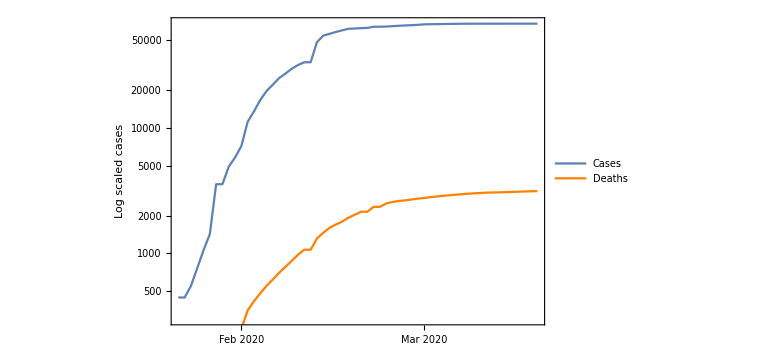

Cases multiplied by 2.7 every 996.19 Days, based on last data from last 20 days

```mathematica
Country = "China";
Province = "Hubei";
ind = Position[Countries,Country][[1,1]];
indProv = Position[States,Province][[1,1]];
ConCasest =Table[ConCases[[ind+1,i]],{i,5,Length[ConCases[[ind+1]]]}];
countrydatacases= Table[{Dates[[i]],ConCasest[[i]]},{i,1,Length[ConCasest]}];
ConDeathst =Table[ConDeaths[[ind+1,i]],{i,5,Length[ConDeaths[[ind+1]]]}];
countrydatadeaths= Table[{Dates[[i]],ConDeathst[[i]]},{i,1,Length[ConDeathst]}];
Show[DateListLogPlot[countrydatacases,PlotLegends->LineLegend[{"Cases"}],DateTicksFormat->{"Day","/","MonthShort"}],DateListLogPlot[countrydatadeaths,PlotStyle->Orange,PlotLegends->LineLegend[{"Deaths"}],PlotRange->All,DateTicksFormat->{"Day","/","MonthShort"}],Frame-> True,FrameLabel->{"","Log scaled cases"},LabelStyle->Directive[16,Black],ImageSize-> Large]
Logcases= Table[{i - (Length[ConCasest]-20),N[Log[ConCasest[[i]]]]},{i,Length[ConCasest]-20,Length[ConCasest]}];
line=Fit[Logcases,{1,x},x];
Print[Style["Cases multiplied by 2.7 every "<> ToString[Round[1/line[[2,1]],0.01]]<>" Days, based on last data from last 20 days ",20,Purple,FontFamily->"Times New Roman"]]
```

```mathematica
(* in China confinement worked and the propagation rate dropped rapidly*)
```

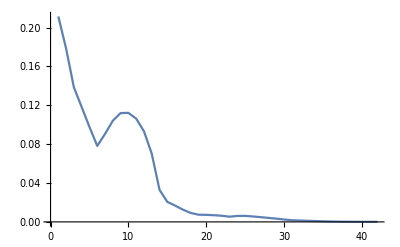

```mathematica
ListLinePlot[Table[Logcases= Table[{i,N[Log[ConCasest[[i]]]]},{i,j,j+7}];
line=Fit[Logcases,{1,x},x][[2,1]],{j,10,Length[ConCasest] - 7}]]
```

## US

Florida

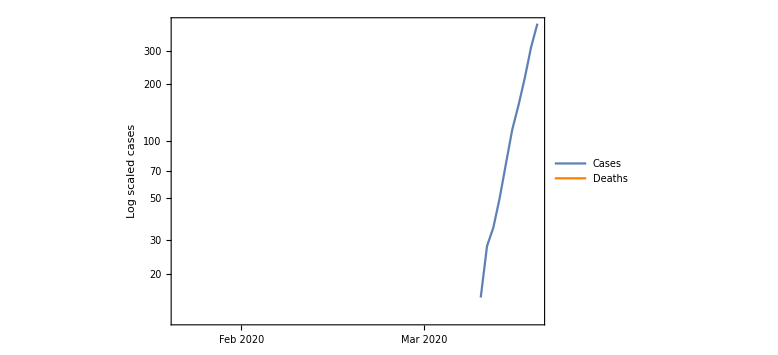

Cases multiplied by 2.7 every 2.95 Days, based on last data from last 5 days

```mathematica
NofDays = 5;(* Number of days the fit routine uses to calculate rate*)
Country = "US";
State = "Florida"
USstates = Table[States [[Position[Countries,Country][[i,1]]]],{i,1,Length[Position[Countries,Country]]}]; (*Remove " ; " to see a list of all states*)
ind = Position[Countries,Country][[Position[USstates,State][[1,1]],1]];
ConCasest =Table[ConCases[[ind+1,i]],{i,5,Length[ConCases[[ind+1]]]}];
countrydatacases= Table[{Dates[[i]],ConCasest[[i]]},{i,1,Length[ConCasest]}];
ConDeathst =Table[ConDeaths[[ind+1,i]],{i,5,Length[ConDeaths[[ind+1]]]}];
countrydatadeaths= Table[{Dates[[i]],ConDeathst[[i]]},{i,1,Length[ConDeathst]}];
Show[DateListLogPlot[countrydatacases,PlotLegends->LineLegend[{"Cases"}],DateTicksFormat->{"Day","/","MonthShort"}],DateListLogPlot[countrydatadeaths,PlotStyle->Orange,PlotLegends->LineLegend[{"Deaths"}],PlotRange->All,DateTicksFormat->{"Day","/","MonthShort"}],Frame-> True,FrameLabel->{"","Log scaled cases"},LabelStyle->Directive[16,Black],ImageSize-> Large]
Logcases= Table[{i - (Length[ConCasest]-NofDays),N[Log[ConCasest[[i]]]]},{i,Length[ConCasest]-NofDays,Length[ConCasest]}];
line=Fit[Logcases,{1,x},x];
Print[Style["Cases multiplied by 2.7 every "<> ToString[Round[1/line[[2,1]],0.01]]<>" Days, based on last data from last " <> ToString[NofDays] <>" days ",20,Purple,FontFamily->"Times New Roman"]]
```

## Germany

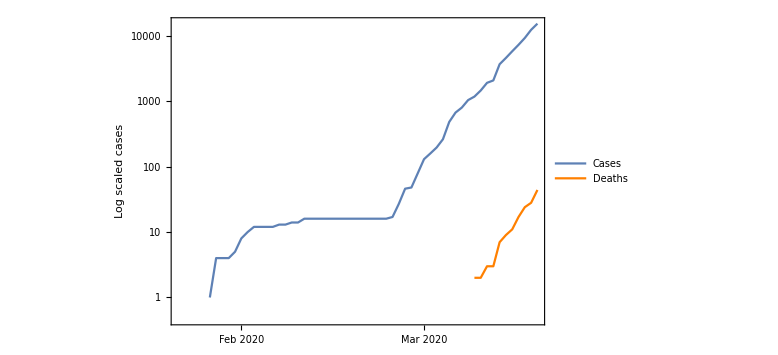

Cases multiplied by 2.7 every 3.92 Days, based on last data from last 15 days

```mathematica
NofDays =15;(* Number of days the fit routine uses to calculate rate*)
Lookfor = "Germany";
ind = Position[Countries,Lookfor][[1,1]];
ConCasest =Table[ConCases[[ind+1,i]],{i,5,Length[ConCases[[ind+1]]]}];
countrydatacases= Table[{Dates[[i]],ConCasest[[i]]},{i,1,Length[ConCasest]}];
ConDeathst =Table[ConDeaths[[ind+1,i]],{i,5,Length[ConDeaths[[ind+1]]]}];
countrydatadeaths= Table[{Dates[[i]],ConDeathst[[i]]},{i,1,Length[ConDeathst]}];
Show[DateListLogPlot[countrydatacases,PlotLegends->LineLegend[{"Cases"}],DateTicksFormat->{"Day","/","MonthShort"}],DateListLogPlot[countrydatadeaths,PlotStyle->Orange,PlotLegends->LineLegend[{"Deaths"}],PlotRange->All,DateTicksFormat->{"Day","/","MonthShort"}],Frame-> True,FrameLabel->{"","Log scaled cases"},LabelStyle->Directive[16,Black],ImageSize-> Large]
Logcases= Table[{i - (Length[ConCasest]-NofDays),N[Log[ConCasest[[i]]]]},{i,Length[ConCasest]-NofDays,Length[ConCasest]}];
line=Fit[Logcases,{1,x},x];
Print[Style["Cases multiplied by 2.7 every "<> ToString[Round[1/line[[2,1]],0.01]]<>" Days, based on last data from last " <> ToString[NofDays] <>" days ",20,Purple,FontFamily->"Times New Roman"]]
```

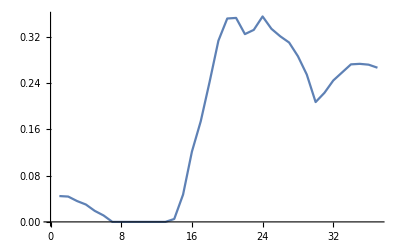

```mathematica
Propagationrate = Table[Logcases= Table[{i,N[Log[ConCasest[[i]]]]},{i,j,j+7}];
line=Fit[Logcases,{1,x},x][[2,1]],{j,15,Length[ConCasest] - 7}];
ListLinePlot[Propagationrate]
```

```mathematica
(* We can calculate roughly based on the slope of the curve how much time of confinement left if the virus keeps spreading like this, x is the number of days of total confinement *)
```

```mathematica
DaysSinceSeriousMeasures =6;
Solve[Fit[Table[Propagationrate[[i]],{i,Length[Propagationrate]-DaysSinceSeriousMeasures,Length[Propagationrate]}],{1,x},x] == 0,x]
```

{{x→-32.2685}}

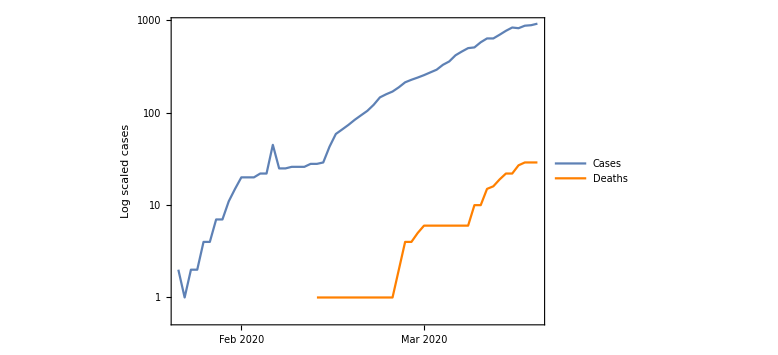

Cases multiplied by 2.7 every 14.55 Days, based on last data from last 15 days

```mathematica
NofDays =15;(* Number of days the fit routine uses to calculate rate*)
Lookfor = "Japan";
ind = Position[Countries,Lookfor][[1,1]];
ConCasest =Table[ConCases[[ind+1,i]],{i,5,Length[ConCases[[ind+1]]]}];
countrydatacases= Table[{Dates[[i]],ConCasest[[i]]},{i,1,Length[ConCasest]}];
ConDeathst =Table[ConDeaths[[ind+1,i]],{i,5,Length[ConDeaths[[ind+1]]]}];
countrydatadeaths= Table[{Dates[[i]],ConDeathst[[i]]},{i,1,Length[ConDeathst]}];
Show[DateListLogPlot[countrydatacases,PlotLegends->LineLegend[{"Cases"}],DateTicksFormat->{"Day","/","MonthShort"}],DateListLogPlot[countrydatadeaths,PlotStyle->Orange,PlotLegends->LineLegend[{"Deaths"}],PlotRange->All,DateTicksFormat->{"Day","/","MonthShort"}],Frame-> True,FrameLabel->{"","Log scaled cases"},LabelStyle->Directive[16,Black],ImageSize-> Large]
Logcases= Table[{i - (Length[ConCasest]-NofDays),N[Log[ConCasest[[i]]]]},{i,Length[ConCasest]-NofDays,Length[ConCasest]}];
line=Fit[Logcases,{1,x},x];
Print[Style["Cases multiplied by 2.7 every "<> ToString[Round[1/line[[2,1]],0.01]]<>" Days, based on last data from last " <> ToString[NofDays] <>" days ",20,Purple,FontFamily->"Times New Roman"]]
```